# F 3 : Agitation Thermique, Vitesse des Molécules et Diffusion

1. Vitesse moyenne d’une molécule

#### 1./ Pour un gaz monoatomique, l’énergie thermique est avec une bonne approximation l’énergie cinétique, Ec, de translation dans l’espace à 3 dimensions, qui est le produit du nombre de degrés de liberté, 3, par la valeur moyenne de l’agitation thermique kT/2par degré de liberté. Calculer la vitesse moyenne instantanée des atomes du gaz qui correspond à la valeur moyenne, Ec. Application numérique avec l’argon à 25 °C

```mathematica
Karvin[T_]:=((T+273.15°C)/(°C)k)
v[T_,M_]:=(√((3*R*T)/M))/.{R->1.9872*4.184 J/(mol*k)}/.{J-> (kg*m^2)/s^2}
t=25°C
Subscript[T, argon]=Karvin[t]
Subscript[M, argon]= 40*10^-3 kg/mol
v[Subscript[T, argon],Subscript[M, argon]]
```

25 °C

298.15 k

kg/(25 mol)

431.186 √(m^2/s^2)

#### 2./ Considérerons de la même façon, que dans un liquide l’énergie cinétique instantanée de translation selon l’axe x d’une molécule de masse m est 1/2 m(v_x)^2, et qu’elle corresponde àkT/2Calculer la vitesse moyenne instantanée de cette molécule dans un liquide. Application numérique avec le lysozyme de masse molaire 14000 à T = 300 K.

```mathematica
Subscript[v, x][T_,M_]:=(√((R*T)/M))/.{R->1.9872*4.184 J/(mol*k)}/.{J-> (kg*m^2)/s^2}
```

```mathematica
Subscript[T, lysozyme]=300k
Subscript[M, lysozyme]=14000kg/mol
Subscript[v, x][Subscript[T, lysozyme],Subscript[M, lysozyme]]
```

300 k

(14000 kg)/mol

0.422098 √(m^2/s^2)

#### Faire un tableau donnant la vitesse moyenne instantanée en fonction de la masse molaire de 14 à 14×10^16grammes de 10 en 10. On utilisera avec profit les fonctions suivantes : Table[] pour générer les valeurs, (noter que vous pouvez générer dans une même liste {i, 14×10^i, la vitesse cherchée} et TableForm[] pour mettre en forme le tableau avec entête et autres indications. Voir l’aide de Mathematica Table[] et TableForm[].

```mathematica
Table[{300k,14*10^i kg/mol},{i,0,16}]
```

```mathematica
TableForm[{{1,2},{3,4}}]
```

```mathematica
Table[Subscript[v, x][300k,14*10^i kg/mol],{i,0,16}]
```

```mathematica
TableForm[{Table[14*10^i kg/mol,{i,0,16}],Table[Subscript[v, x][300k,14*10^i kg/mol],{i,0,16}]},TableDirections->Row]
```

(14 kg)/mol | 13.3479 √(m^2/s^2)
(140 kg)/mol | 4.22098 √(m^2/s^2)
(1400 kg)/mol | 1.33479 √(m^2/s^2)
(14000 kg)/mol | 0.422098 √(m^2/s^2)
(140000 kg)/mol | 0.133479 √(m^2/s^2)
(1400000 kg)/mol | 0.0422098 √(m^2/s^2)
(14000000 kg)/mol | 0.0133479 √(m^2/s^2)
(140000000 kg)/mol | 0.00422098 √(m^2/s^2)
(1400000000 kg)/mol | 0.00133479 √(m^2/s^2)
(14000000000 kg)/mol | 0.000422098 √(m^2/s^2)
(140000000000 kg)/mol | 0.000133479 √(m^2/s^2)
(1400000000000 kg)/mol | 0.0000422098 √(m^2/s^2)
(14000000000000 kg)/mol | 0.0000133479 √(m^2/s^2)
(140000000000000 kg)/mol | 4.22098×10^-6 √(m^2/s^2)
(1400000000000000 kg)/mol | 1.33479×10^-6 √(m^2/s^2)
(14000000000000000 kg)/mol | 4.22098×10^-7 √(m^2/s^2)
(140000000000000000 kg)/mol | 1.33479×10^-7 √(m^2/s^2)

2. Énergie cinétique de gaz monoatomiques

#### Un mélange gazeux comporte de l’hélium (MM = 4) et du radon (MM = 222). Quel est celui qui a le plus d’énergie cinétique ?

```mathematica
Ec[T_,M_]:=(3*R*T)/(2*M)/.{R->1.9872*4.184 J/(mol*k)}
```

```mathematica
Subscript[Ec, helium]=Ec[300k,4kg/mol]
Subscript[Ec, radon]=Ec[300k,222kg/mol]
```

(935.375 J)/kg

(16.8536 J)/kg

Donc, énergie cinétique d’helium est plus élevée.

#### Calculer la vitesse moyenne d’un atome d’hélium et de radon à la même température (T = 300 K).

```mathematica
Subscript[v, helium]=v[300k,4kg/mol]
Subscript[v, radon]=v[300k,222kg/mol]
```

43.2522 √(m^2/s^2)

5.80579 √(m^2/s^2)

3. L’agitation thermique à l’origine de la pression osmotique

#### Loi de van’t Hoff sur la pression osmotique : π = RT C : “À l’équilibre, la pression osmotique, π, exercée par une solution diluée sur la membrane semi-perméable la séparant de son solvant pur, est numériquement égale à celle qu’exerceraient les moles du soluté si elles constituaient un gaz parfait dans le volume V de la solution à la même température.” Peut-on dire que π est le résultat des chocs exercés par les molécules de soluté imperméant ?

#### En quoi π est différent de P ?

La formule de la pression osmotique d’une solution idéale développée par van’t Hoff 
π V = - R T ln(1-γ*x)
π = (x R T)/V = C R T

Oui, on peut dire que π est le résultat des chocs exercés par les molécules de soluté imperméant. Car si la membrane semi-perméable est remplacé par imperméable, le pression osmotique n’existe plus. Avec la membrane semi-perméable, dans le même temperature, selon la formule de la pression osmotique, on peut facilement déduire π_1/π_2 =C_1/C_2, la pression osmotique est dépendant de la concentration.

La pression osmotique est différent que P, car π est une phénomène de la force intermoléculaire, par contre, P est de la gravitation.

4. Marche aléatoire Gare d’Austerlitz - Jussieu - Quai Saint-Michel

#### A./ La démarche statistique

Pour bien comprendre la nature des mouvements moléculaires et leurs enseignements de statistique, un groupe
d’étudiants entreprend une marche aléatoire au départ de Jussieu sur le trajet entre la Gare d’Austerlitz et le Quai
Saint-Michel. On suppose que la Gare d’Austerlitz et le Quai Saint-Michel sont de part et d’autre de Jussieu à 1 km
de distance sur un trajet rectiligne orienté (une dimension).

#### 1./ Ils parcourent en marchant normalement d’abord la distance Jussieu - Quai Saint-Michel (ou Gare d’Austerlitz) à la vitesse de 1 m/s soit 3.6 km/h. Combien de temps leur faut-il ?

```mathematica
t[d_,v_]:=d/v
```

```mathematica
t[1km,3.6km/h]
```

0.277778 h

#### 2./ Pour l’étape de marche aléatoire, les règles de déplacement sont les suivantes. La vitesse de déplacement reste de 1 m/s, mais la direction du déplacement change aléatoirement (par exemple à l’aide d’un tirage pile ou face). En partant de Jussieu, combien de temps faut-il pour atteindre ou dépasser le Quai Saint-Michel ou la Gare d’Austerlitz avec une probabilité de 15.87*2 = 31.74 % ?

#### On peut s’aider des questions suivantes : a./ soit X la variable aléatoire qui donne la distance de déplacement. X suit une suit une loi binomiale, qui tend vers une loi normale centrée sur Jussieu, et d’écart-type s. Quelle est cette loi normale en donnant l’espérance de X et sa variance en fonction du nombre de tirage pile ou face, N.

#### b./ on cherche N tel que : P(»x» > x1) = 31.74 % où x1=1000 m.

X suit la loi normal, f(x,N)=1/(√(2π)σ)e^(-1/2((x-μ)/σ)^2)ou μ=0,σ=√N l
On cherche σ tel que :
P (|x|>X_1=1000)=P(x<-x_1)+P(x>x_1)
=P((x-μ)/σ<(-x_1-μ)/σ)+P((x-μ)/σ>(x_1-μ)/σ)
=P(u<-u_1)+P(u>u_1)
= 2*(1-F(u_1))=0.3174
1-F(u_1)=0.1587
F(u_1)=0.8413
u_1=1= x_1/σ=(1km)/σ

σ= 1000m=√N l ou l = 1m

```mathematica
Solve[1000m==√N 1m,N]
```

{{N→1000000}}

#### B./ La démarche expérimentale avec Mathematica

Un autre groupe d’étudiants entreprend des calculs beaucoup moins fatigants avec Mathematica.
Note importante aux programmeurs C : nous ne testerons que des opérations, et il n’y a rien à mettre en mémoire,
ni à déclarer. Donc : pas besoin d’écrire toto = opération[]. Il suffit de faire opération[].

#### 1./ Progression par tirage au hasard {-1, +1} : tracés de trajectoires au hasard

#### Utiliser la fonction RandomChoice[] (cf. aide) pour effectuer un tirage -1 ou +1 (on avance de -1 ou 1) : il faut donc mettre les bons arguments dans RandomChoice[]. Vérifier que cela fonctionne bien.

```mathematica
(*RandomChoice[{1,2,3}]
RandomChoice[{1,2,3},4]
RandomChoice[{1,2,3,4}->{1,2,3,4}]*)
RandomChoice[{-1,1},10]
```

{-1,-1,-1,-1,-1,1,1,1,-1,1}

#### Pour obtenir une idée de la trajectoire, il faut obtenir la liste des sommes cumulées. Il existe une fonction idéale pour cela : FoldList[] (cf. aide). Tester pour une fonction arbitraire, partant de 0 :

```mathematica
FoldList[f,0,{a,b,c}]
```

{0,f[0,a],f[f[0,a],b],f[f[f[0,a],b],c]}

#### Tester la fonction Plus, partant de 0 :

```mathematica
FoldList[Plus,0,{a,b,c}]
```

{0,a,a+b,a+b+c}

#### Il faut donc réaliser cette dernière opération avec la liste produite par RandomChoice[] (au lieu de {a, b, c}). Tester

```mathematica
randomWalk[i_]:=FoldList[Plus,0,RandomChoice[{-1,1},10^i]]
```

#### Tracer la trajectoire avec ListPlot[]. On pourra utiliser l’option Joined->True pour joindre les points. Noter que le tracé est directement effectué en fonction du nombre numéro du tirage dans la liste, donc en fonction du temps ici.

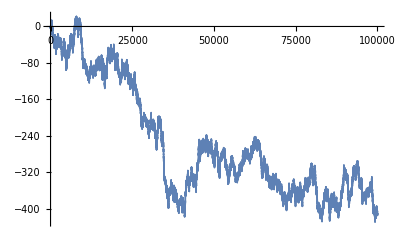

```mathematica
ListPlot[randomWalk[5]]
```

#### Relancer plusieurs fois la fonction, et constater qu’il faut un très grand nombre d’essais pour avoir une chance de dépasser 1000. Nous allons maintenant étudier ce point.

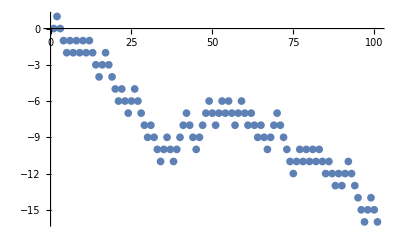

```mathematica
ListPlot[randomWalk[2]]
```

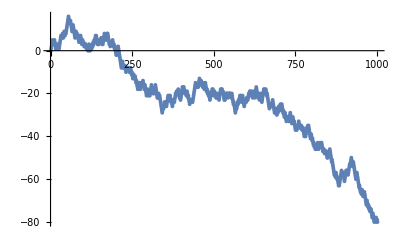

```mathematica
ListPlot[randomWalk[3]]
```

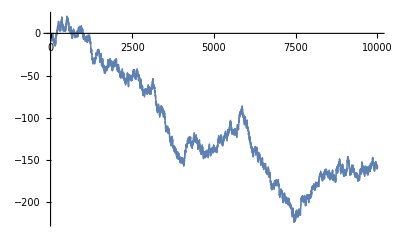

```mathematica
ListPlot[randomWalk[4]]
```

#### 2./ Relation entre le point d’arrivée et le nombre de tirages.

Cherchons maintenant à établir une relation empirique entre le point d’arrivée, et le nombre de tirages.
(Nous ne nous intéressons plus au ListPlot[] ci-dessus)

#### On peut très facilement ne regarder que le dernier point de la liste, i.e. le point d’arrivée, avec Fold[] au lieu de FoldList[]. Tester pour RandomChoice[{-1,1}, 10000], i.e. 10000 tirages. Dans la suite nous allons utiliser 10^n tirages, et faire varier n de 1 à 7.

```mathematica
randomArrival[i_]:=(Fold[Plus,0,RandomChoice[{-1,1},10^i]])
```

```mathematica
TableForm[Table[Table[randomArrival[i],{i,{1,2,3,4,5,6,7}}],{j,0,6}]]
```

2 | -10 | 18 | -6 | -288 | -54 | -1070
-4 | 12 | 24 | -164 | -158 | 996 | -1418
-2 | 0 | -38 | -26 | 574 | -502 | 5886
6 | -4 | -14 | 118 | 386 | -1178 | -3674
-6 | 0 | 0 | -26 | -232 | -1010 | 1520
10 | 4 | -38 | 18 | 192 | -40 | 1318
2 | -18 | -2 | 4 | -24 | -1242 | -1820

#### Constituons donc avec Table[] une liste de 100 points d’arrivée de 10^n tirages pour n variant de 1 à 7. En faisant plusieurs essais, on observe qu’il faut environ 10^6 tirages ou plus pour dépasser 1000 en valeur absolue. Nous allons préciser ce point.

```mathematica
TableForm[Table[Table[randomArrival[i],{i,{1,2,3,4,5,6,7}}],{j,1,100}],TableDirections->Row]
```

-2 | 0 | -2 | 0 | -6 | 4 | 4 | 2 | -6 | -4 | 0 | 0 | 2 | 2 | -4 | 2 | 0 | 0 | -6 | 0 | -4 | -6 | 0 | 4 | 4 | -4 | -4 | -2 | -6 | 0 | -4 | 4 | 0 | -2 | -4 | -6 | 4 | 0 | -4 | -2 | 2 | -2 | -2 | 6 | 2 | 6 | 0 | 0 | -2 | -2 | 4 | -4 | -6 | 2 | -6 | -8 | 2 | -6 | -4 | -2 | -2 | -2 | -2 | 0 | -4 | 2 | -2 | -2 | 0 | 2 | -6 | 0 | 0 | 2 | -2 | -2 | 0 | -4 | 2 | -2 | -2 | -6 | 0 | 0 | 2 | -2 | 4 | 2 | 4 | 2 | -2 | -2 | -4 | -10 | 0 | 4 | 2 | -2 | 4 | -2
2 | 10 | -4 | 18 | -8 | -14 | 8 | 4 | -14 | 12 | 2 | -14 | -2 | -6 | -12 | -18 | 12 | 2 | 2 | 2 | 0 | 12 | -4 | 10 | 2 | 10 | 2 | 2 | -8 | 16 | 12 | 2 | -12 | -10 | -2 | 2 | 10 | 6 | 0 | -8 | -20 | -12 | 10 | 8 | 14 | 14 | 8 | 18 | -8 | -8 | 8 | -6 | -2 | 8 | -8 | -4 | 16 | -6 | 2 | -16 | -8 | 12 | 2 | 18 | 4 | 2 | -6 | -16 | 0 | -2 | -8 | -8 | 4 | 14 | 12 | 0 | -10 | -8 | -10 | 2 | 14 | -16 | 0 | 2 | 4 | -12 | -20 | 20 | 14 | 4 | -14 | 8 | -2 | 2 | -22 | -14 | -12 | 12 | -2 | 4
-38 | 24 | -40 | 6 | -36 | -20 | -10 | 32 | 18 | -24 | -40 | 14 | 40 | 48 | 12 | -34 | 46 | -34 | 26 | -20 | -34 | 4 | 14 | 2 | -84 | 10 | 14 | 26 | 52 | 64 | -10 | -40 | -10 | 12 | 8 | -74 | -24 | -30 | -10 | 40 | 2 | 40 | 22 | -28 | -48 | -28 | -4 | 6 | 46 | 0 | -30 | -44 | -2 | 2 | -30 | 8 | 6 | 50 | -12 | 12 | -2 | -2 | 76 | -4 | -22 | -22 | 20 | 10 | 14 | 26 | 4 | -16 | 28 | 40 | -40 | -16 | -58 | -44 | 60 | -2 | -38 | -26 | 32 | -34 | 8 | 10 | 14 | -58 | -16 | -18 | -54 | 0 | 10 | -36 | -2 | -32 | -22 | 12 | 12 | -64
-34 | -70 | 160 | -24 | -140 | -94 | 56 | -58 | -20 | -20 | 38 | 0 | -18 | -6 | 28 | -112 | -160 | 156 | -216 | -110 | -46 | -32 | -50 | 196 | -28 | -64 | -50 | -92 | 38 | 82 | 122 | -54 | 6 | -8 | -64 | -60 | 26 | 6 | 18 | -68 | -94 | 46 | 60 | 192 | -64 | -32 | -154 | 78 | -22 | -62 | 34 | -46 | 22 | 20 | 150 | 26 | 34 | -36 | 182 | 174 | 6 | -120 | -88 | 2 | 84 | -112 | -84 | 172 | 22 | 230 | 108 | 24 | 134 | 138 | -30 | 58 | -60 | 132 | 32 | 44 | -20 | 72 | -20 | 80 | 8 | -230 | 14 | -48 | -246 | -164 | 48 | -88 | -148 | 16 | -196 | -18 | -24 | -186 | -130 | -80
-196 | 8 | -258 | 124 | -12 | 240 | 76 | 92 | -214 | -70 | -236 | 214 | 324 | -418 | -380 | -412 | 220 | 594 | 224 | -734 | -292 | 158 | -20 | -626 | -812 | 174 | -628 | -324 | 44 | -400 | 120 | -794 | -506 | 98 | -432 | -954 | -146 | 414 | 332 | -246 | -62 | -626 | 414 | -150 | -148 | -160 | 14 | -98 | 112 | -392 | -180 | 126 | -346 | -288 | -266 | 322 | -196 | 32 | 14 | 128 | 392 | -118 | 110 | -56 | -30 | -226 | 144 | 50 | 282 | 208 | 362 | -482 | -596 | 108 | -278 | -68 | 294 | -32 | -150 | -288 | -18 | -72 | -322 | 174 | 226 | 224 | -200 | 480 | 122 | -10 | -88 | 258 | -268 | 196 | 356 | -156 | 310 | 18 | -316 | 18
272 | -212 | 774 | -320 | -240 | 832 | -1200 | -170 | -1550 | -1872 | -860 | 416 | -2036 | -988 | 470 | 338 | -1260 | 346 | 2104 | 950 | 1786 | 2 | -220 | 710 | -1452 | -1074 | 448 | 766 | -194 | 1586 | 898 | 148 | 1180 | -500 | -992 | 396 | -74 | 1326 | -2986 | 1728 | -198 | 1140 | 1132 | 598 | 846 | -864 | -474 | -760 | 2566 | -1742 | -376 | 286 | -132 | -728 | -764 | -1108 | -184 | -444 | -1996 | -942 | 1862 | 324 | 1776 | -1394 | 8 | -586 | -692 | 742 | 82 | -1982 | 10 | -1494 | -566 | -784 | 576 | -648 | 678 | -226 | 1570 | -1258 | 146 | 1880 | 1258 | -336 | -12 | 376 | -1102 | -304 | -1366 | 76 | 268 | -760 | -1056 | -1528 | -322 | -46 | -80 | -432 | -170 | -766
4062 | -2182 | -82 | -4016 | 334 | -5014 | -2012 | -1000 | -2964 | -1148 | 164 | 636 | -4894 | -1876 | 1030 | 840 | -366 | -790 | -322 | 2726 | 840 | 3764 | -2230 | 2268 | -764 | -942 | -182 | 390 | 8066 | -504 | -1606 | 1072 | -1560 | 912 | -564 | 724 | 232 | 2228 | 9284 | -2476 | -2520 | 500 | 3820 | -1368 | -3578 | 404 | -1258 | 1976 | -1530 | 880 | -8128 | 1276 | 426 | -1826 | 432 | 1862 | -2518 | -1086 | -1466 | 7718 | 5922 | -1680 | 2444 | -1914 | 2186 | 3092 | 3220 | 3068 | -5526 | 1416 | -726 | 1000 | 86 | -1750 | -2776 | -5244 | -7426 | 2420 | -938 | 2366 | 3876 | 366 | 3064 | -404 | 1958 | -3462 | -8690 | -1044 | 458 | -1362 | 1808 | -304 | 1330 | 1020 | -4896 | 3326 | 1950 | 2200 | -418 | 1802

```mathematica
Transpose[%19]
```

{{-2,0,-2,0,-6,4,4,2,-6,-4,0,0,2,2,-4,2,0,0,-6,0,-4,-6,0,4,4,-4,-4,-2,-6,0,-4,4,0,-2,-4,-6,4,0,-4,-2,2,-2,-2,6,2,6,0,0,-2,-2,4,-4,-6,2,-6,-8,2,-6,-4,-2,-2,-2,-2,0,-4,2,-2,-2,0,2,-6,0,0,2,-2,-2,0,-4,2,-2,-2,-6,0,0,2,-2,4,2,4,2,-2,-2,-4,-10,0,4,2,-2,4,-2},{2,10,-4,18,-8,-14,8,4,-14,12,2,-14,-2,-6,-12,-18,12,2,2,2,0,12,-4,10,2,10,2,2,-8,16,12,2,-12,-10,-2,2,10,6,0,-8,-20,-12,10,8,14,14,8,18,-8,-8,8,-6,-2,8,-8,-4,16,-6,2,-16,-8,12,2,18,4,2,-6,-16,0,-2,-8,-8,4,14,12,0,-10,-8,-10,2,14,-16,0,2,4,-12,-20,20,14,4,-14,8,-2,2,-22,-14,-12,12,-2,4},{-38,24,-40,6,-36,-20,-10,32,18,-24,-40,14,40,48,12,-34,46,-34,26,-20,-34,4,14,2,-84,10,14,26,52,64,-10,-40,-10,12,8,-74,-24,-30,-10,40,2,40,22,-28,-48,-28,-4,6,46,0,-30,-44,-2,2,-30,8,6,50,-12,12,-2,-2,76,-4,-22,-22,20,10,14,26,4,-16,28,40,-40,-16,-58,-44,60,-2,-38,-26,32,-34,8,10,14,-58,-16,-18,-54,0,10,-36,-2,-32,-22,12,12,-64},{-34,-70,160,-24,-140,-94,56,-58,-20,-20,38,0,-18,-6,28,-112,-160,156,-216,-110,-46,-32,-50,196,-28,-64,-50,-92,38,82,122,-54,6,-8,-64,-60,26,6,18,-68,-94,46,60,192,-64,-32,-154,78,-22,-62,34,-46,22,20,150,26,34,-36,182,174,6,-120,-88,2,84,-112,-84,172,22,230,108,24,134,138,-30,58,-60,132,32,44,-20,72,-20,80,8,-230,14,-48,-246,-164,48,-88,-148,16,-196,-18,-24,-186,-130,-80},{-196,8,-258,124,-12,240,76,92,-214,-70,-236,214,324,-418,-380,-412,220,594,224,-734,-292,158,-20,-626,-812,174,-628,-324,44,-400,120,-794,-506,98,-432,-954,-146,414,332,-246,-62,-626,414,-150,-148,-160,14,-98,112,-392,-180,126,-346,-288,-266,322,-196,32,14,128,392,-118,110,-56,-30,-226,144,50,282,208,362,-482,-596,108,-278,-68,294,-32,-150,-288,-18,-72,-322,174,226,224,-200,480,122,-10,-88,258,-268,196,356,-156,310,18,-316,18},{272,-212,774,-320,-240,832,-1200,-170,-1550,-1872,-860,416,-2036,-988,470,338,-1260,346,2104,950,1786,2,-220,710,-1452,-1074,448,766,-194,1586,898,148,1180,-500,-992,396,-74,1326,-2986,1728,-198,1140,1132,598,846,-864,-474,-760,2566,-1742,-376,286,-132,-728,-764,-1108,-184,-444,-1996,-942,1862,324,1776,-1394,8,-586,-692,742,82,-1982,10,-1494,-566,-784,576,-648,678,-226,1570,-1258,146,1880,1258,-336,-12,376,-1102,-304,-1366,76,268,-760,-1056,-1528,-322,-46,-80,-432,-170,-766},{4062,-2182,-82,-4016,334,-5014,-2012,-1000,-2964,-1148,164,636,-4894,-1876,1030,840,-366,-790,-322,2726,840,3764,-2230,2268,-764,-942,-182,390,8066,-504,-1606,1072,-1560,912,-564,724,232,2228,9284,-2476,-2520,500,3820,-1368,-3578,404,-1258,1976,-1530,880,-8128,1276,426,-1826,432,1862,-2518,-1086,-1466,7718,5922,-1680,2444,-1914,2186,3092,3220,3068,-5526,1416,-726,1000,86,-1750,-2776,-5244,-7426,2420,-938,2366,3876,366,3064,-404,1958,-3462,-8690,-1044,458,-1362,1808,-304,1330,1020,-4896,3326,1950,2200,-418,1802}}

#### 3./ Moyenne et écart-type de 100 trajectoires de 10^n tirages, en fonction de n

Nous allons étudier la moyenne et l’écart-type de 100 trajectoires de 10^n tirages, en fonction de n.
Les étapes du calcul sont les suivantes :

#### a. Générer à l’aide de Table[] une liste de 100 points d’arrivée de 10^n tirages. (Tester avec /. n->2 en le mettant au bon endroit dans l’expression !)

#### b. Calculer la moyenne (ou l’écart-type) de cette liste au moyen de Mean[] (ou de StandardDeviation[]) pour n variant 1 à 5.

NB : pour n variant de 1 à 5 : le temps de calcul est de l’ordre de la seconde ; pour n= 6 compter environ 10
secondes

```mathematica
trajRepeat[i_,n_]:=(Table[randomArrival[i],{k,1,n}])
```

```mathematica
TableForm[Table[{Mean[trajRepeat[i,100]],StandardDeviation[trajRepeat[i,100]]},{i,2,5}]]//N
```

0.52 | 10.5586
-1.9 | 33.0943
11.16 | 111.45
48.36 | 317.273

#### Quelles sont vos conclusions :

pour la moyenne ?
		pour l’écart-type ?

La moyenne reste appriximate à 0, la variance éleve. Autant que n augmente, le random marche arrive plus en plus loin du point orginal.

#### c. Tracer avec ListPlot[] la moyenne (ou l’écart-type) en fonction de 10^n (n variant 1 à 6). (il faut simplement constituer une liste du type : Table[ {10^n, moyenne}, {n, 1, 5,1}]). Dans la suite nous n’étudierons que l’écart-type.

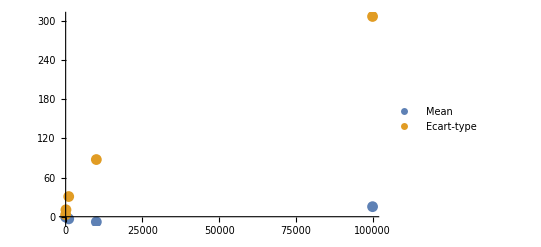

```mathematica
ListPlot[{Table[{10^i,Mean[trajRepeat[i,100]]},{i,1,5}],Table[{10^i,StandardDeviation[trajRepeat[i,100]]},{i,1,5}]},PlotLegends->{"Mean","Ecart-type"}]
```

#### d. Modifier l’expression précédente pour l’écart-type, pour obtenir une relation linéaire (Suggestion : prendre le carré de l’écart-type).

On pourra superposer le graphique avec le tracé de l’équation d’une droite

(obtenu avec Plot[x, {x, 0, 10}], PlotStyle → DashedE)
Il suffit de mettre les expressions des deux tracés dans une liste {}, et de mettre le tout dans Show[], pour mettre à l’échelle. Tester plusieurs fois. Quand concluez vous ?

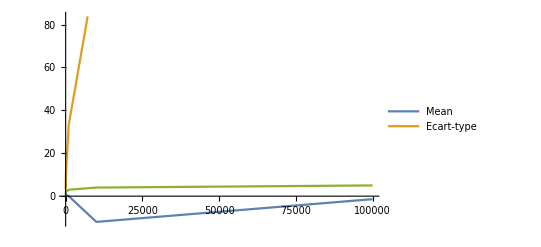

```mathematica
ListPlot[{Table[{10^i,Mean[trajRepeat[i,100]]},{i,1,5}],Table[{10^i,StandardDeviation[trajRepeat[i,100]]},{i,1,5}],Table[{10^i,i},{i,1,5}]},PlotLegends->{"Mean","Ecart-type"},Joined->{True}]
```

#### 4./ Exploration avec un histogramme

Reprenons tout depuis le début. Nous savons désormais qu’il faut environ 10^6 tirages aléatoires pour avoir de bonnes chances de dépasser le Quai Saint-Michel ou la gare d’Austerlitz (plus d’1 km de Jussieu).
Nous ne nous intéressons plus qu’au point d’arrivée au bout de 10^6 tirages : n est donc fixé à 6. Attention : les calculs prennent environ 10 secondes pour 100 trajectoires. Pour tester, prendre n <= 5.

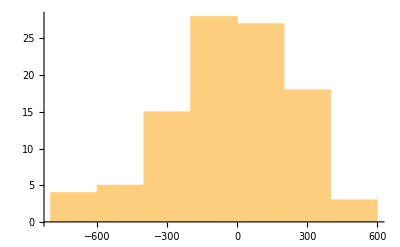

```mathematica
Histogram[Table[randomArrival[5],{i,1,100}]]
```

#### a. Générer une liste de 100 trajectoires de point d’arrivée (n = 6).

(NB : au lieu de Fold[Plus, 0, maListeAMoi], on peut aussi faire Apply[Plus, maListeAMoi], mais Fold est 2 fois plus rapide !)
(NB : On peut aussi utiliser la fonction dédiée Total[maListeAMoi] étrangement un peu moins rapide que Fold)

```mathematica
randomMarche[i_]:=Apply[Plus,RandomChoice[{-1,1},10^i]]
```

```mathematica
Table[randomMarche[6],{i,1,100}]
```

{552,476,-634,-218,-1046,-954,202,-822,-826,470,-1690,2472,-662,-458,-676,0,1168,122,-454,-584,-724,8,1720,1552,-672,1190,-86,230,-1036,-618,-1300,-660,1482,-718,848,-1578,496,590,126,510,-1730,-286,-512,-2688,-640,714,-686,-1668,-54,-648,704,1834,-2376,-1908,-6,926,-218,156,-254,-1366,400,-200,930,-1760,-614,4,1006,1202,58,-628,426,14,2030,-676,2,32,312,-98,334,-1130,-1336,-1156,1140,2012,-478,1006,790,-1200,-738,-1030,1104,-370,-1130,882,356,1410,570,262,-268,570}

#### b. Faire un histogramme de cette liste avec Histogram[] (Pour 1000 trajectoires compter entre 30 s et 1 minute).

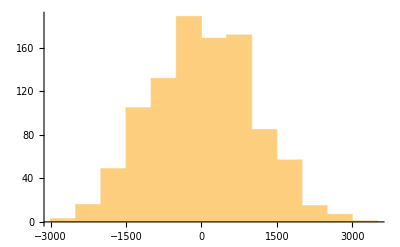

```mathematica
Histogram[Table[randomMarche[6],{i,1,1000}]]
```

5. Diffusion d’une macromolécule

#### Une molécule de la taille de l’albumine (MM=60000) est caractérisée par un coefficient de diffusion, D_1 = 6.1 *(10^-7)cm^2/s. Elle se trouve en un point donné A d’une solution. Quelle est la probabilité de trouver cette molécule à l’extérieur de la sphère de centre A et de rayon 19μ au bout d’une seconde? Que vous inspire ce résultat ? (NB :D_3 = 3 D_1)

Remarque : le problème est équivalent à celui d’un expérimentateur qui cherche à insérer un soluté coloré dans une cellule avec une micropipette

```mathematica
Subscript[D, 1]=6.1*(10^-7)
Subscript[D, 3]=3*Subscript[D, 1]
σ=√(2*Subscript[D, 3]*1)
rayon=19*10^-6
Probability[x>rayon,x\[Distributed]NormalDistribution[0,σ]]
```

6.1×10^-7

1.83×10^-6

0.00191311

19/1000000

0.496038

La probabilité que cette molécule se trouve à l’extérieur de la sphère de centre A est très élevé dans une seconde. Tant que t augmente, la probabilité devient plus en plus proche de 50%

6. Diffusion dans un gaz

#### Un flacon de parfum ouvert agit comme une source ponctuelle de molécules de parfum qui diffusent dans l’air, D_1= 10^-5 m^2/s = 0.1 cm^2/s. Elle se trouve au centre O d’une pièce A d’une solution. Quelle est la valeur de σ au bout de t = 1s, 100s, 10000s ? (NB : D_3 = 3 D_1)

```mathematica
Subscript[D, 1]=10^-5 m^2/s
Subscript[D, 3]=3*Subscript[D, 1]
Table[√(2*Subscript[D, 3]*t),{t,{1s,100s,10000s}}]//N
```

m^2/(100000 s)

(3 m^2)/(100000 s)

{0.00774597 √(m^2),0.0774597 √(m^2),0.774597 √(m^2)}

7. Diffusion dans une membrane

#### Un phospholipide diffuse latéralement dans la membrane bicouche d’un liposome de diamètre d = 100 nm avec un coefficient de diffusion, D_1 = 10^-8 cm^2/s. Que pouvez-vous dire sur la vitesse de diffusion de ce phospholipide à la surface du liposome ? (mêmes questions que l’exercice précédent)

Cette question est une diffusion en deux dimension. Donc on a :

```mathematica
circle[diametre_]:=(π*diametre)//N;
Subscript[D, 1]=Quantity[10^-10,"m^2/s"];
Subscript[D, 2]=2*Subscript[D, 1];
d=Quantity[100,"nm"];
time2D[σ_]:=(σ^2/(2*Subscript[D, 2]));
distance=circle[d]/2;
t=time2D[distance]//N;
v=UnitConvert[distance,"cm"]/t//N
```

0.254648